# 2D First-Passage time

## Drift towards the equilibrium at (x, xh) = (0, 0) with an absorbing boundary at x=0 and reflecting boundary at xh=0.

### Nondimensionalize space with x*=1

```mathematica
tf=20;
xf=20;
```

## Write down the Fokker-Planck equation

```mathematica
FP= D[p[x,xh,  t], t]== λ*xh*D[p[x,xh, t], x] -κ2 *x*D[p[x,xh,t], xh]+κ1*D[xh*p[x, xh, t], xh]+(σg^2/2)*D[p[x, xh, t], {x, 2}]+(σξ^2*κ2^2/2)*D[p[x, xh, t], {xh, 2}]
```

p^(0,0,1)[x,xh,t]==-x κ2 p^(0,1,0)[x,xh,t]+κ1 (p[x,xh,t]+xh p^(0,1,0)[x,xh,t])+1/2 κ2^2 σξ^2 p^(0,2,0)[x,xh,t]+xh λ p^(1,0,0)[x,xh,t]+1/2 σg^2 p^(2,0,0)[x,xh,t]

## Choose the parameter values

```mathematica
params  = {
{λ->0.1, σg->2, σξ->0.4, κ1->2, κ2->2}, 
{λ->0.2, σg->2, σξ->0.4, κ1->2, κ2->2}, 
{λ->0.4, σg->2, σξ->0.4, κ1->2, κ2->2}
(*{λ->3, σg->1, σξ->0.4, κ1->2, κ2->5}*)
}
```

{{λ→0.1,σg→2,σξ→0.4,κ1→2,κ2→2},{λ→0.2,σg→2,σξ→0.4,κ1→2,κ2→2},{λ→0.4,σg→2,σξ→0.4,κ1→2,κ2→2}}

## Write down the boundary conditions

```mathematica
bcs = {p[-xf, xh, t]==0,
           p[xf, xh, t]==0,
           p[x, xf, t]==0,
           p[x, 1, t]==0
	     (*D[p[x, xh, t]]==NeumannValue[0, xh==0]*)
(*(D[p[x, xh, t], xh]/.xh->0 )== 0,
(D[p[x, xh, t], xh]/.xh->xf )== 0,
(D[p[x, xh, t], x]/.x->xf)== 0*)
}
```

{p[-20,xh,t]==0,p[20,xh,t]==0,p[x,20,t]==0,p[x,1,t]==0}

## And initial condition (distribution with the s.s. covariance, depends on parameters)

```mathematica
ic0 = PDF[MultinormalDistribution[{10, 10},({{σg^2/(2 κ1)+(κ1 σg^2)/(2 κ2 λ)+(κ2 λ σξ^2)/(2 κ1),σg^2/(2 λ)},{σg^2/(2 λ),(κ2 σg^2)/(2 κ1 λ)+(κ2^2 σξ^2)/(2 κ1)}}/.params[[1]])], {x, xh}]
```

0.0328163 ⅇ^(1/2 (-(-10+x) (0.857096 (-10+x)-0.850294 (-10+xh))-(-0.850294 (-10+x)+0.893149 (-10+xh)) (-10+xh)))

```mathematica
NDSolverParams[ic_, param_] :=Module[{N},
N = NDSolve[Join[{(FP/. param),p[x,xh, 0]== ic0}, bcs],
                                   p,{t,0,tf},{x, -xf,xf},{xh, 1,xf}, 
Method->{"MethodOfLines","TemporalVariable"->t, "SpatialDiscretization"->"FiniteElement"}];
Return[p/.N[[1]]];
]
```

```mathematica
sols=MapThread[NDSolverParams, {ic, params}]
```

{InterpolatingFunction[…],InterpolatingFunction[{{-20., 20.}, {1., 20.}, {0., 20.}}, <>],InterpolatingFunction[{{-20., 20.}, {1., 20.}, {0., 20.}}, <>]}

```mathematica
Manipulate[Plot3D[sols[[1]][x, xh, t], {x, 0,xf}, {xh, 1,xf}, PlotRange->{-0.01, 0.1}], {t, 0, tf}]
Manipulate[Plot3D[sols[[2]][x, xh, t], {x, 0,xf}, {xh, 1, xf}, PlotRange->{-0.01, 0.1}], {t, 0, tf}]
Manipulate[Plot3D[sols[[3]][x, xh, t], {x, 0,xf}, {xh, 1, xf}, PlotRange->{-0.01, 0.1}], {t, 0, tf}]
```

## Integrate to get survival probability

```mathematica
nint1[t_?NumericQ]:=Module[{x, xh},NIntegrate[sols[[1]][x,xh,t], {x,xh}∈sols[[1]]["ElementMesh"]]];
nint2[t_?NumericQ]:=Module[{x, xh},NIntegrate[sols[[2]][x,xh,t], {x,xh}∈sols[[2]]["ElementMesh"]]];
nint3[t_?NumericQ]:=Module[{x, xh},NIntegrate[sols[[3]][x,xh,t], {x,xh}∈sols[[3]]["ElementMesh"]]];
trange = N[Range[0, tf, tf/50]];
```

```mathematica
S1 = Table[nint1[tp], {tp, trange}];
S2 = Table[nint2[tp], {tp, trange}];
S3 = Table[nint3[tp], {tp, trange}];
```

```mathematica
s1=Interpolation[Transpose@{trange, S1}]
s2=Interpolation[Transpose@{trange, S2}]
s3=Interpolation[Transpose@{trange, S3}]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
l = {"λ=0.5", "λ=1","λ=2"}
```

{λ=0.5,λ=1,λ=2}

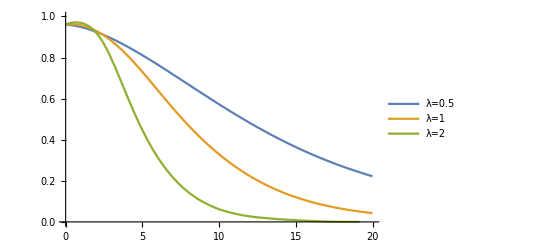

```mathematica
Plot[{s1[t], s2[t], s3[t]},{t, 0, tf}, PlotLegends->l, PlotRange->{0,1}]
```

## Get first-passage time probability

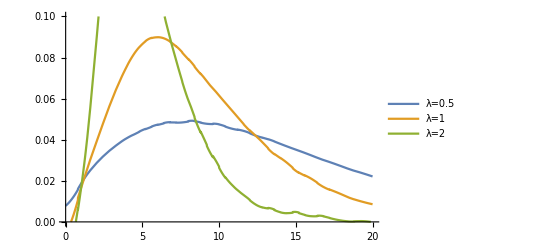

```mathematica
Plot[{-s1'[t], -s2'[t],- s3'[t]},{t, 0, tf}, PlotRange->{0, 0.1} ,PlotLegends->l]
```

```mathematica
NIntegrate[-s1'[t], {t, 0, tf}]
NIntegrate[-s2'[t], {t, 0, tf}]
NIntegrate[-s3'[t], {t, 0, tf}]

NIntegrate[-t*s1'[t], {t, 0, tf}]
NIntegrate[-t*s2'[t], {t, 0, tf}]
NIntegrate[-t*s3'[t], {t, 0, tf}]

NIntegrate[-t*t*s1'[t], {t, 0, tf}]
NIntegrate[-t*t*s2'[t], {t, 0, tf}]
NIntegrate[-t*t*s3'[t], {t, 0, tf}]
```

1.05396

0.987679

1.00006

2.80366

1.09442

0.529231

10.0526

0.956396

0.30875

## Plots and scaling

## Behavior with v near crossover

```mathematica
x0Constant = 2
vCrossover = N[x0Constant*Erfc[x0Constant]]
vRange = Reverse[N[PowerRange[5*^-5,2*^-2 , 3]]]
 DConstant = 0.5
 kConstant = 1
```

2

0.00935547

{0.01215,0.00405,0.00135,0.00045,0.00015,0.00005}

0.5

1

```mathematica
results =FPT[DConstant,kConstant, x0Constant, #]&/@vRange
```

General::munfl: -5.07352×10^-307 (-0.0140515) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -5.07352×10^-307 0.0140515 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -5.07352×10^-307 (-0.00702576) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]}}

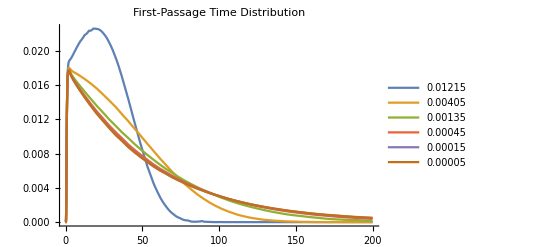

```mathematica
Plot[results, {t, 0, 200}, PlotRange->All, PlotLegends->vRange, PlotLabel->"First-Passage Time Distribution"]
```

## Behavior with x0 near crossover

```mathematica
x0Range = Range[1, 7, 1]
vConstant = 1*^-3
x0Crossover = FindRoot[vConstant - x*(1-Erf[x]), {x, 2}]
 DConstant = 0.5
kConstant = 1
```

{1,2,3,4,5,6,7}

1/1000

{x→2.50348}

0.5

1

```mathematica
results =FPT[DConstant,kConstant, #, vConstant]&/@x0Range
```

General::munfl: 3.29208×10^-306 (-0.00629723) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.93187×10^-308 (-0.00629723) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -4.08071×10^-308 (-0.00629723) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]}}

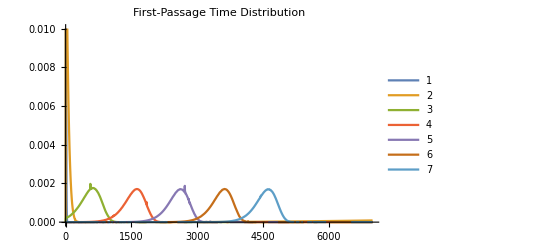

```mathematica
Plot[results, {t, 0, 7000}, PlotLegends->x0Range, PlotLabel->"First-Passage Time Distribution", PlotRange->{0, 0.01}]
```

#### Scaling with D

```mathematica
Clear[x0, d, v, k]
vConstant = 0.01
 DRange = PowerRange[0.1, 45, 2.7]
 kConstant = 1
x0Constant = 15
DCrossover = NSolve[(x0Constant/vConstant )== 1/Erfc[Sqrt[kConstant/(2*d)]*x0Constant], d]
```

0.01

{0.1,0.27,0.729,1.9683,5.31441,14.3489,38.742}

1

15

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{d→19.4301}}

```mathematica
results =FPT[#,kConstant, x0Constant, vConstant]&/@DRange
```

General::munfl: -9.57366×10^-308 (-0.00747168) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -9.57366×10^-308 0.00747168 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -9.57366×10^-308 (-0.00373584) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]}}

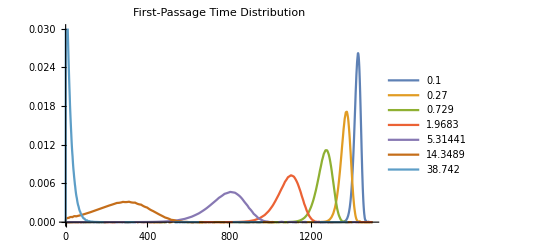

```mathematica
Plot[results, {t, 0, 1500}, PlotLegends->DRange, PlotLabel->"First-Passage Time Distribution", PlotRange->{0, 0.03}]
```